# RB-SFA: High Harmonic Generation in the Strong Field Approximation via Mathematica

© Emilio Pisanty 2014-2016. Licensed under GPL and CC-BY-SA.

## Quantum-orbit functionality (experimental)

The following is a suite of functions to calculate HHG spectra via quantum-orbit calculations, i.e. by using the saddle-point approximation on both temporal integrals. This function suite has been used for production calculations, and in general it is trustworthy in the results it produces. However, the details of the interface should not be considered fixed and are subject to later change; hence the mark as experimental for the time being. In addition, the documentation presented in this document is still under construction: the examples below show a reasonably complete use case from getting the action through to calculating a spectrum, at present with no explanatory text beyond the usage messages of the different functions. Further documentation will be added at a later date.

### Specifications

The goal for this part of the package is to calculate the Fourier transform directly,

          D(Ω)=ⅈ∫_(-∞)^∞ ⅆt∫_(-∞)^t ⅆt'((2π)/(ϵ+ⅈ τ))^(3/2) d(π(p_s(t,t-t'),t)) × F(t')·d(π(p_s(t,t'),t'))×exp[-ⅈ S(p_s(t,t'),t,t')]×ⅇ^(+ⅈ Ω t),

via a saddle-point approximation on the ionization and recombination times t' and t, which gives a harmonic dipole of the form

          D(Ω)=ⅈ∑_s √((2π)^2/(ⅈ^2 det(∂_(t,t')^2 (S(t,t'))_s)))((2π)/(ϵ+ⅈ (t_s-t'_s)))^(3/2) d(π(p_s(t_s,t_s-t'_s),t_s)) × F(t'_s)·d(π(p_s(t_s,t'_s),t'_s))×exp[-ⅈ S(p_s(t_s,t'_s),t_s,t'_s)]×ⅇ^(+ⅈ Ω t_s),

where the times t_s and t'_s (and equivalently τ_s=t_s-t'_s) are obtained via the saddle-point equations

          (∂S)/(∂t')(t_s,t'_s)=0, (∂S)/(∂t)(t_s,t'_s)=Ω,

as described in detail in the original paper by Lewenstein et al. (Phys. Rev. A 49 no. 3, 2117 (1994)), or in e.g. M. Ivanov and O. Smirnova. Multielectron high harmonic generation: simple man on a complex plane. In T. Schultz and M. Vrakking (eds.), Attosecond and XUV Physics: Ultrafast Dynamics and Spectroscopy, pp. 201–256 (Wiley-VCH, Weinheim, 2014), arXiv:1304.2413.

### Getting the action and prefactor

```mathematica
Quit
```

```mathematica
parameters={F->√int 0.053,ω->45.6/λ,int->1,λ->800,Ip->getIonizationPotential["Helium",0]};
```

```mathematica
AbsoluteTiming[
{prefactor,S}=makeDipoleList[
VectorPotential->Function[t,{0,0,F/ω Cos[ω t]}],FieldParameters->parameters
,CarrierFrequency->(ω//.parameters),IonizationPotential->(Ip//.parameters)
,DipoleTransitionMatrixElement->{hydrogenicDTMERegularized,hydrogenicDTME}
,Verbose->3
,Simplifier->Simplify
]
]
```

{0.06818,{{(0.+0. ⅈ) (1/(0.1+ⅈ (#1-#2)))^(3/2) (0.929825 Cos[0.057 #2]-(16.3127 Sin[0.057 #1]-16.3127 Sin[0.057 #2])/((0.-0.1 ⅈ)+#1-#2)),(0.+0. ⅈ) (1/(0.1+ⅈ (#1-#2)))^(3/2) (0.929825 Cos[0.057 #2]-(16.3127 Sin[0.057 #1]-16.3127 Sin[0.057 #2])/((0.-0.1 ⅈ)+#1-#2)),((0.+47.5253 ⅈ) Sin[0.057 #2] (1/(0.1+ⅈ (#1-#2)))^(3/2) (0.929825 Cos[0.057 #1]-(16.3127 Sin[0.057 #1]-16.3127 Sin[0.057 #2])/((0.-0.1 ⅈ)+#1-#2)) (0.929825 Cos[0.057 #2]-(16.3127 Sin[0.057 #1]-16.3127 Sin[0.057 #2])/((0.-0.1 ⅈ)+#1-#2)))/(1.807+(0.929825 Cos[0.057 #1]-(16.3127 Sin[0.057 #1]-16.3127 Sin[0.057 #2])/((0.-0.1 ⅈ)+#1-#2))^2)^3}&,1/2 (3.79199 Sin[0.114 #1]-3.79199 Sin[0.114 #2]+0.432287 #1+(1.807+(16.3127 Sin[0.057 #1]-16.3127 Sin[0.057 #2])^2/((0.-0.1 ⅈ)+#1-1. #2)^2) (#1-#2)-(532.209 (1. Sin[0.057 #1]-1. Sin[0.057 #2])^2)/((0.-0.1 ⅈ)+#1-1. #2)-0.432287 #2)&}}

```mathematica
S[t,tt]
```

1/2 (0.432287 t-0.432287 tt+3.79199 Sin[0.114 t]+(t-tt) (1.807+(16.3127 Sin[0.057 t]-16.3127 Sin[0.057 tt])^2/((0.-0.1 ⅈ)+t-1. tt)^2)-(532.209 (1. Sin[0.057 t]-1. Sin[0.057 tt])^2)/((0.-0.1 ⅈ)+t-1. tt)-3.79199 Sin[0.114 tt])

```mathematica
prefactor[t,tt]//Simplify
```

{0,0,((0.+47.5253 ⅈ) (1/(0.1+ⅈ (t-tt)))^(3/2) Sin[0.057 tt] (0.929825 Cos[0.057 t]+(-16.3127 Sin[0.057 t]+16.3127 Sin[0.057 tt])/((0.-0.1 ⅈ)+t-1. tt)) (0.929825 Cos[0.057 tt]+(-16.3127 Sin[0.057 t]+16.3127 Sin[0.057 tt])/((0.-0.1 ⅈ)+t-1. tt)))/((1.807+(0.929825 Cos[0.057 t]+(-16.3127 Sin[0.057 t]+16.3127 Sin[0.057 tt])/((0.-0.1 ⅈ)+t-1. tt))^2)^3)}

```mathematica
$HistoryLength=10;
LaunchKernels[16-Length[Kernels[]]];
```

### Getting saddle points

```mathematica
?GetSaddlePoints
```

GetSaddlePoints[Ω,S,{tmin,tmax},{τmin,τmax}] finds a list of solutions {t,τ} of the HHG temporal saddle-point equations at harmonic energy Ω for action S, in the range {tmin, tmax} of recombination time and {τmin, τmax} of excursion time, where both ranges should be the lower-left and upper-right corners of rectangles in the complex plane.

GetSaddlePoints[ΩRange,S,{tmin,tmax},{τmin,τmax}] finds solutions of the HHG temporal saddle-point equations for a range of harmonic energies ΩRange, and returns an Association with each harmonic energy Ω indexing a list of saddle-point solution pairs {t,τ}.

GetSaddlePoints[Ωspec,S,{{{tmin_1,tmax_1},{τmin_1,τmax_1}},{{tmin_2,tmax_2},{τmin_2,τmax_2}},…}] uses multiple time domains and combines the solutions.

GetSaddlePoints[Ωspec,S,{{urange,vrange},…},IndependentVariables→{u,v}] uses the explicit independent variables u and v to solve the equations and over the given ranges, where u and v can be any of "RecombinationTime", "IonizationTime" and "ExcursionTime", or their shorthands "t", "tt" and "τ" resp.

```mathematica
DateString[]
Block[{ω,Ip,κ,U,γ},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
ΩRange=Range[Ceiling[Ip,ω],Ceiling[1.32Ip+3.17U]+5ω,0.1ω];

saddlePoints=GetSaddlePoints[ΩRange,S,{
{{(0°-1.5ⅈ γ)/ω,(450°+1.5ⅈ γ)/ω},{(-90°+0.6ⅈ γ)/ω,(0°+1.2ⅈ γ)/ω}},
{{(180°)/ω+(0°-1.5ⅈ γ)/ω,(180°)/ω+(450°+1.5ⅈ γ)/ω},{(180°)/ω+(-90°+0.6ⅈ γ)/ω,(180°)/ω+(0°+1.2ⅈ γ)/ω}}
},IndependentVariables->{"t","tt"}
,Tolerance->10^-5/ω,Seeds->75
,Jacobian->FiniteDifference
]
]⟦1;;3⟧//AbsoluteTiming
DateString[]
```

Wed 11 May 2016 21:49:03

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

RBSFA`GetSaddlePoints::error: Errors encountered for frequency Ω=1.4706.

{13.4445,<|0.912→{{63.7226-14.708 ⅈ,27.8501-40.9741 ⅈ},{8.60697-14.708 ⅈ,27.8501-40.9741 ⅈ},{12.2456-11.286 ⅈ,31.4941-37.5465 ⅈ},{67.3613-11.286 ⅈ,31.4941-37.5465 ⅈ},{137.474+0.11658 ⅈ,108.706-20.4102 ⅈ},{82.3584+0.11658 ⅈ,108.706-20.4102 ⅈ},{87.3152+0.120837 ⅈ,113.662-20.406 ⅈ},{142.431+0.120837 ⅈ,113.662-20.406 ⅈ},{184.91-0.232336 ⅈ,154.386-20.9851 ⅈ},{129.795-0.232336 ⅈ,154.386-20.9851 ⅈ},{134.957-0.211504 ⅈ,159.548-20.9644 ⅈ},{190.073-0.211504 ⅈ,159.548-20.9644 ⅈ}},0.9177→{{63.2741-15.2318 ⅈ,27.3882-41.4809 ⅈ},{8.15841-15.2318 ⅈ,27.3882-41.4809 ⅈ},{12.8665-10.8162 ⅈ,32.1077-37.053 ⅈ},{67.9821-10.8162 ⅈ,32.1077-37.053 ⅈ},{136.77+0.117763 ⅈ,107.992-20.4101 ⅈ},{81.6545+0.117763 ⅈ,107.992-20.4101 ⅈ},{88.0875+0.123561 ⅈ,114.424-20.4045 ⅈ},{143.203+0.123561 ⅈ,114.424-20.4045 ⅈ},{128.998-0.237015 ⅈ,153.598-20.9882 ⅈ},{184.114-0.237015 ⅈ,153.598-20.9882 ⅈ},{190.815-0.209637 ⅈ,160.297-20.9612 ⅈ},{135.699-0.209637 ⅈ,160.297-20.9612 ⅈ}},0.9234→{{7.81051-15.6581 ⅈ,27.0265-41.8909 ⅈ},{62.9262-15.6581 ⅈ,27.0265-41.8909 ⅈ},{68.5012-10.4436 ⅈ,32.6205-36.6562 ⅈ},{13.3856-10.4436 ⅈ,32.6205-36.6562 ⅈ},{81.0858+0.119053 ⅈ,107.413-20.41 ⅈ},{136.201+0.119053 ⅈ,107.413-20.41 ⅈ},{143.842+0.126278 ⅈ,115.052-20.403 ⅈ},{88.7262+0.126278 ⅈ,115.052-20.403 ⅈ},{128.341-0.241246 ⅈ,152.949-20.9908 ⅈ},{183.457-0.241246 ⅈ,152.949-20.9908 ⅈ},{136.301-0.208306 ⅈ,160.906-20.9585 ⅈ},{191.416-0.208306 ⅈ,160.906-20.9585 ⅈ}}|>}

Wed 11 May 2016 21:49:17

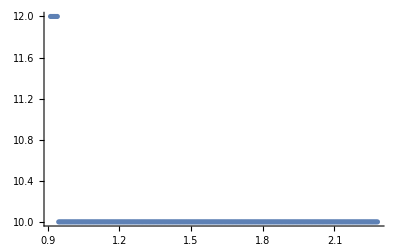

```mathematica
ListPlot[Length/@saddlePoints⟦1;;-1⟧]
```

```mathematica
With[{data=Compress[saddlePoints]},
Button["Restore example saddle points",Set[saddlePoints,Uncompress[saddlePoints]];saddlePoints;]
]
```

Restore example saddle points

### Global saddle-points map

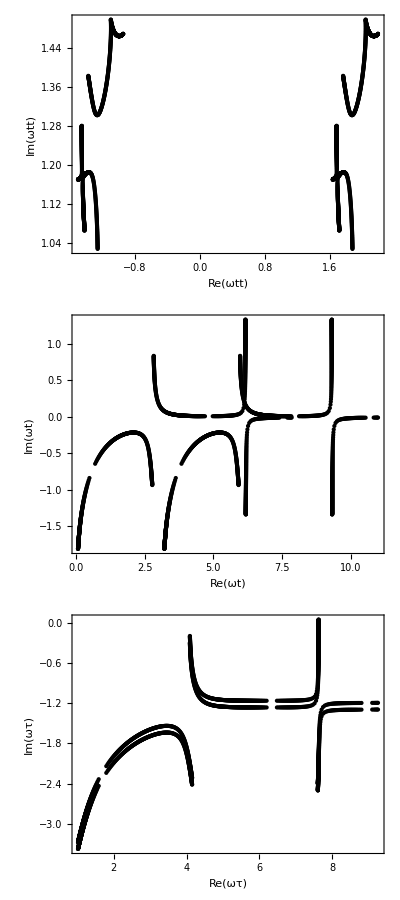

```mathematica
Block[{ω,Ip,κ,U,γ,saddles},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
saddles=saddlePoints;
Column[{
Show[
Graphics[{
Table[
Map[
Apply[Function[{t,τ},
Tooltip[Point[ReIm[ω (t-τ)]],{Ω/ω,ω{t,τ},Floor[ω Re[t-τ],π]/π}]
]],saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωtt)","Im(ωtt)"}
]
,Show[
Graphics[{
Table[
Map[
Apply[Function[{t,τ},
Tooltip[Point[ReIm[ω t]],{Ω/ω,ω{t,τ},Floor[ω Re[t-τ],π]/π}]
]],saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,Show[
Graphics[{
Table[
Map[
Apply[Function[{t,τ},
Tooltip[Point[ReIm[ω τ+ 0.1 ⅈ Floor[ω Re[t-τ],π]/π]],{Ω/ω,ω{t,τ},Floor[ω Re[t-τ],π]/π}]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωτ)","Im(ωτ)"}
]
}]
]
```

### Syntax options for GetSaddlePoints

Single energy, single range:

```mathematica
Block[{ω,Ip,κ,U,γ},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
ΩRange=Range[Ceiling[Ip,ω]+ω,Ceiling[1.32Ip+3.17U]+ω,2ω];

GetSaddlePoints[ΩRange⟦1⟧,S,{(0-1.5ⅈ γ)/ω,(3π+1.5ⅈ γ)/ω},{(0-2.5ⅈ γ)/ω,(2π+2.5ⅈ γ)/ω}
,Tolerance->10^-5/ω,Seeds->30
,SelectionFunction->Function[{t,τ,SS,Ω},Im[t-τ]>0]
,IndependentVariables->{"tt","τ"}
,IndependentVariables->{"RecombinationTime","ExcursionTime"}
]
]
```

{{61.3283-17.8854 ⅈ,25.3117-44.0085 ⅈ},{171.56-17.8854 ⅈ,25.3117-44.0085 ⅈ},{71.4328-8.63528 ⅈ,35.5268-34.6444 ⅈ},{181.664-8.63528 ⅈ,35.5268-34.6444 ⅈ},{126.549-8.63528 ⅈ,35.5268-34.6444 ⅈ},{133.234+0.130964 ⅈ,104.361-20.4077 ⅈ},{243.466+0.130964 ⅈ,104.361-20.4077 ⅈ}}

Single energy, multiple ranges:

```mathematica
Block[{ω,Ip,κ,U,γ},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
ΩRange=Range[Ceiling[Ip,ω]+ω,Ceiling[1.32Ip+3.17U]+ω,2ω];

GetSaddlePoints[ΩRange⟦1⟧,S,{{{(0-1.5ⅈ γ)/ω,(3π+1.5ⅈ γ)/ω},{(0-2.5ⅈ γ)/ω,(2π+2.5ⅈ γ)/ω}},{{(0-1.5ⅈ γ)/ω,(3π+1.5ⅈ γ)/ω},{(2π-2.5ⅈ γ)/ω,(4π+2.5ⅈ γ)/ω}}}
,Tolerance->10^-5/ω,Seeds->30
,SelectionFunction->Function[{t,τ,SS,Ω},Im[t-τ]>0]
,IndependentVariables->{"tt","τ"}
,IndependentVariables->{"RecombinationTime","ExcursionTime"}
]
]
```

{{116.444-17.8854 ⅈ,25.3117-44.0085 ⅈ},{126.549-8.63528 ⅈ,35.5268-34.6444 ⅈ},{71.4328-8.63528 ⅈ,35.5268-34.6444 ⅈ},{181.664-8.63528 ⅈ,35.5268-34.6444 ⅈ},{188.35+0.130964 ⅈ,104.361-20.4077 ⅈ},{243.466+0.130964 ⅈ,104.361-20.4077 ⅈ},{202.548+0.150768 ⅈ,118.55-20.3896 ⅈ},{147.432+0.150768 ⅈ,118.55-20.3896 ⅈ},{290.012-0.272736 ⅈ,149.346-21.0081 ⅈ},{194.593-0.203933 ⅈ,164.14-20.9434 ⅈ},{249.708-0.203933 ⅈ,164.14-20.9434 ⅈ},{304.824-0.203933 ⅈ,164.14-20.9434 ⅈ},{242.257+0.0334796 ⅈ,214.037-20.4209 ⅈ}}

List of energies, single range:

```mathematica
Block[{ω,Ip,κ,U,γ},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
ΩRange=Range[Ceiling[Ip,ω]+ω,Ceiling[1.32Ip+3.17U]+ω,2ω];

GetSaddlePoints[ΩRange⟦1;;2⟧,S,{(0-1.5ⅈ γ)/ω,(3π+1.5ⅈ γ)/ω},{(0-2.5ⅈ γ)/ω,(2π+2.5ⅈ γ)/ω}
,Tolerance->10^-5/ω,Seeds->30
,SelectionFunction->Function[{t,τ,SS,Ω},Im[t-τ]>0]
,IndependentVariables->{"tt","τ"}
,IndependentVariables->{"RecombinationTime","ExcursionTime"}
]
]
```

<|0.969→{{61.3283-17.8854 ⅈ,25.3117-44.0085 ⅈ},{171.56-17.8854 ⅈ,25.3117-44.0085 ⅈ},{71.4328-8.63528 ⅈ,35.5268-34.6444 ⅈ},{181.664-8.63528 ⅈ,35.5268-34.6444 ⅈ},{126.549-8.63528 ⅈ,35.5268-34.6444 ⅈ},{133.234+0.130964 ⅈ,104.361-20.4077 ⅈ},{243.466+0.130964 ⅈ,104.361-20.4077 ⅈ}},1.083→{{59.5902-21.0124 ⅈ,23.275-46.9513 ⅈ},{169.822-21.0124 ⅈ,23.275-46.9513 ⅈ},{131.403-6.48193 ⅈ,40.4479-31.9638 ⅈ},{186.519-6.48193 ⅈ,40.4479-31.9638 ⅈ},{239.05+0.168505 ⅈ,99.7229-20.3967 ⅈ},{128.819+0.168505 ⅈ,99.7229-20.3967 ⅈ}}|>

List of energies, multiple ranges:

```mathematica
Block[{ω,Ip,κ,U,γ},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
ΩRange=Range[Ceiling[Ip,ω]+ω,Ceiling[1.32Ip+3.17U]+ω,2ω];

GetSaddlePoints[ΩRange⟦1;;2⟧,S,{{{(0-1.5ⅈ γ)/ω,(3π+1.5ⅈ γ)/ω},{(0-2.5ⅈ γ)/ω,(2π+2.5ⅈ γ)/ω}},{{(0-1.5ⅈ γ)/ω,(3π+1.5ⅈ γ)/ω},{(2π-2.5ⅈ γ)/ω,(4π+2.5ⅈ γ)/ω}}}
,Tolerance->10^-5/ω,Seeds->30
,SelectionFunction->Function[{t,τ,SS,Ω},Im[t-τ]>0]
,IndependentVariables->{"tt","τ"}
,IndependentVariables->{"RecombinationTime","ExcursionTime"}
]
]
```

<|0.969→{{116.444-17.8854 ⅈ,25.3117-44.0085 ⅈ},{126.549-8.63528 ⅈ,35.5268-34.6444 ⅈ},{71.4328-8.63528 ⅈ,35.5268-34.6444 ⅈ},{181.664-8.63528 ⅈ,35.5268-34.6444 ⅈ},{188.35+0.130964 ⅈ,104.361-20.4077 ⅈ},{243.466+0.130964 ⅈ,104.361-20.4077 ⅈ},{133.234+0.130964 ⅈ,104.361-20.4077 ⅈ},{202.548+0.150768 ⅈ,118.55-20.3896 ⅈ},{147.432+0.150768 ⅈ,118.55-20.3896 ⅈ},{290.012-0.272736 ⅈ,149.346-21.0081 ⅈ},{194.593-0.203933 ⅈ,164.14-20.9434 ⅈ},{249.708-0.203933 ⅈ,164.14-20.9434 ⅈ},{304.824-0.203933 ⅈ,164.14-20.9434 ⅈ},{242.257+0.0334796 ⅈ,214.037-20.4209 ⅈ}},1.083→{{114.706-21.0124 ⅈ,23.275-46.9513 ⅈ},{186.519-6.48193 ⅈ,40.4479-31.9638 ⅈ},{131.403-6.48193 ⅈ,40.4479-31.9638 ⅈ},{76.2875-6.48193 ⅈ,40.4479-31.9638 ⅈ},{183.935+0.168505 ⅈ,99.7229-20.3967 ⅈ},{128.819+0.168505 ⅈ,99.7229-20.3967 ⅈ},{239.05+0.168505 ⅈ,99.7229-20.3967 ⅈ},{154.268+0.278908 ⅈ,125.093-20.3022 ⅈ},{209.383+0.278908 ⅈ,125.093-20.3022 ⅈ},{283.079-0.408886 ⅈ,142.658-21.0949 ⅈ},{309.722-0.206451 ⅈ,169.188-20.9196 ⅈ},{254.606-0.206451 ⅈ,169.188-20.9196 ⅈ},{199.49-0.206451 ⅈ,169.188-20.9196 ⅈ},{237.464+0.0449743 ⅈ,209.127-20.4165 ⅈ}}|>

### Reperioding of saddle points

#### Getting saddle points over a t,τ box including multiple ionization bursts

```mathematica
DateString[]
Block[{ω,Ip,κ,U,γ},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;


ΩRange=Range[Ceiling[Ip,ω],Ceiling[1.32Ip+3.17U]+5ω,0.1ω];

saddlePoints=GetSaddlePoints[ΩRange,S,{(0°-1.5ⅈ γ)/ω,(2π+1.5ⅈ γ)/ω},{(0-2.5ⅈ γ)/ω,(3π+0.1ⅈ γ)/ω}
,Tolerance->10^-5/ω,Seeds->300
,SelectionFunction->Function[{t,τ,SS,Ω},Im[t-τ]>0]
]
]⟦1;;3⟧//AbsoluteTiming
DateString[]
```

Wed 11 May 2016 13:43:26

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

GetSaddlePoints::error: Errors encountered for frequency Ω=1.0716

{26.1461,<|0.912→{{8.60697-14.708 ⅈ,27.8501-40.9741 ⅈ},{63.7226-14.708 ⅈ,27.8501-40.9741 ⅈ},{67.3613-11.286 ⅈ,31.4941-37.5465 ⅈ},{12.2456-11.286 ⅈ,31.4941-37.5465 ⅈ},{27.2427+0.11658 ⅈ,108.706-20.4102 ⅈ},{82.3584+0.11658 ⅈ,108.706-20.4102 ⅈ},{32.1996+0.120837 ⅈ,113.662-20.406 ⅈ},{87.3152+0.120837 ⅈ,113.662-20.406 ⅈ},{19.5634-0.232336 ⅈ,154.386-20.9851 ⅈ},{74.6791-0.232336 ⅈ,154.386-20.9851 ⅈ},{79.8412-0.211504 ⅈ,159.548-20.9644 ⅈ},{24.7256-0.211504 ⅈ,159.548-20.9644 ⅈ}},0.9177→{{63.2741-15.2318 ⅈ,27.3882-41.4809 ⅈ},{8.15841-15.2318 ⅈ,27.3882-41.4809 ⅈ},{12.8665-10.8162 ⅈ,32.1077-37.053 ⅈ},{67.9821-10.8162 ⅈ,32.1077-37.053 ⅈ},{26.5389+0.117763 ⅈ,107.992-20.4101 ⅈ},{81.6545+0.117763 ⅈ,107.992-20.4101 ⅈ},{32.9718+0.123561 ⅈ,114.424-20.4045 ⅈ},{88.0875+0.123561 ⅈ,114.424-20.4045 ⅈ},{18.7672-0.237015 ⅈ,153.598-20.9882 ⅈ},{73.8828-0.237015 ⅈ,153.598-20.9882 ⅈ},{25.4677-0.209637 ⅈ,160.297-20.9612 ⅈ},{80.5833-0.209637 ⅈ,160.297-20.9612 ⅈ}},0.9234→{{7.81051-15.6581 ⅈ,27.0265-41.8909 ⅈ},{62.9262-15.6581 ⅈ,27.0265-41.8909 ⅈ},{68.5012-10.4436 ⅈ,32.6205-36.6562 ⅈ},{13.3856-10.4436 ⅈ,32.6205-36.6562 ⅈ},{81.0858+0.119053 ⅈ,107.413-20.41 ⅈ},{25.9702+0.119053 ⅈ,107.413-20.41 ⅈ},{88.7262+0.126278 ⅈ,115.052-20.403 ⅈ},{33.6106+0.126278 ⅈ,115.052-20.403 ⅈ},{73.2256-0.241246 ⅈ,152.949-20.9908 ⅈ},{18.1099-0.241246 ⅈ,152.949-20.9908 ⅈ},{81.1851-0.208306 ⅈ,160.906-20.9585 ⅈ},{26.0694-0.208306 ⅈ,160.906-20.9585 ⅈ}}|>}

Wed 11 May 2016 13:43:52

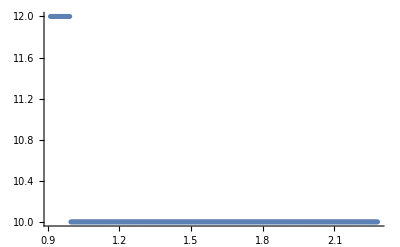

```mathematica
ListPlot[Length/@saddlePoints]
```

```mathematica
With[{data=Compress[saddlePoints]},
Button["Restore saddlePoints",Set[saddlePoints,Uncompress[data]]]
]
```

```mathematica
saddlePoints;
```

#### Global saddle-points map

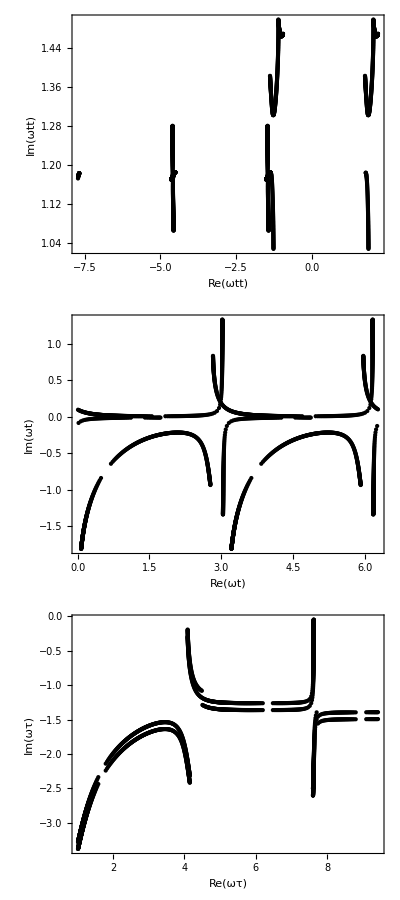

```mathematica
Block[{ω,Ip,κ,U,γ,saddles},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
saddles=saddlePoints;
Column[{
Show[
Graphics[{
Point[
Flatten[Table[
Map[
Apply[Function[{t,τ},
ReIm[ω (t-τ)]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}],1]
]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωtt)","Im(ωtt)"}
]
,Show[
Graphics[{
Point[
Flatten[Table[
Map[
Apply[Function[{t,τ},
ReIm[ω t]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}],1]
]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,Show[
Graphics[{
Point[
Flatten[Table[
Map[
Apply[Function[{t,τ},
ReIm[ω τ+ 0.1 ⅈ Floor[ω Re[t-τ],π]/π]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}],1]
]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωτ)","Im(ωτ)"}
]
}]
]
```

#### Reperioding a saddle-point set

```mathematica
?ReperiodSaddles
```

ReperiodSaddles[{{t_1,τ_1},{t_2,τ_2},…},f] readjusts the assigned cycle of the saddle points {t_i,τ_i}, returning the list {{t_1+f[t_1,τ_1],τ_1},…}.

ReperiodSaddles[<|Ω_1→{{t_11,τ_11},…},Ω_2→…|>,f] reperiods saddle-point pairs in a harmonic-energy-indexed association.

ReperiodSaddles[<|label_l→<|Ω_1→{{t_11,τ_11},…},…|>,…|>,f] reperiods saddle-point pairs of a classified set of saddle points.

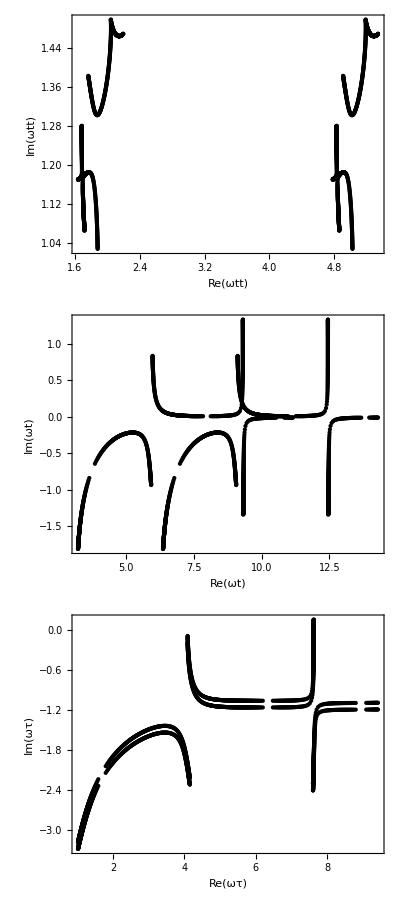

```mathematica
Block[{ω,Ip,κ,U,γ,saddles},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
saddles=ReperiodSaddles[saddlePoints,Function[{t,τ},{t-Floor[Re[t-τ],(2π)/ω],τ}]];
Column[{
Show[
Graphics[{
Point[
Flatten[Table[
Map[
Apply[Function[{t,τ},
ReIm[ω (t-τ)]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}],1]
]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωtt)","Im(ωtt)"}
]
,Show[
Graphics[{
Point[
Flatten[Table[
Map[
Apply[Function[{t,τ},
ReIm[ω t]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}],1]
]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,Show[
Graphics[{
Point[
Flatten[Table[
Map[
Apply[Function[{t,τ},
ReIm[ω τ+ 0.1 ⅈ Floor[ω Re[t-τ],π]/π]
]]
,saddles[Ω]⟦All⟧]
,{Ω,Keys[saddles]}],1]
]
}]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωτ)","Im(ωτ)"}
]
}]
]
```

### Saddle-point classification

#### Classified saddles using points-based map

```mathematica
?ClassifyQuantumOrbits
```

ClassifyQuantumOrbits[saddlePoints,f] sorts an indexed set of saddle points of the form <|Ω_1→{{t_11,τ_11},{t_12,τ_12},…}…|> using a function f, which should turn f[t,τ,Ω] into an appropriate label, and returns an association of the form <|label_1→<|Ω_1→<|1→{t,τ},2→{t,τ},…|>,…|>,…|>.

ClassifyQuantumOrbits[saddlePoints,f,sortFunction] uses the function sortFunction to sort the sets of saddle points {{t_11,τ_11},{t_12,τ_12},…} for each label and harmonic energy.

ClassifyQuantumOrbits[saddlePoints,f,sortFunction,DiscardedLabels→{label_1,label_2,…}] specifies a list of labels to discard from the final output.

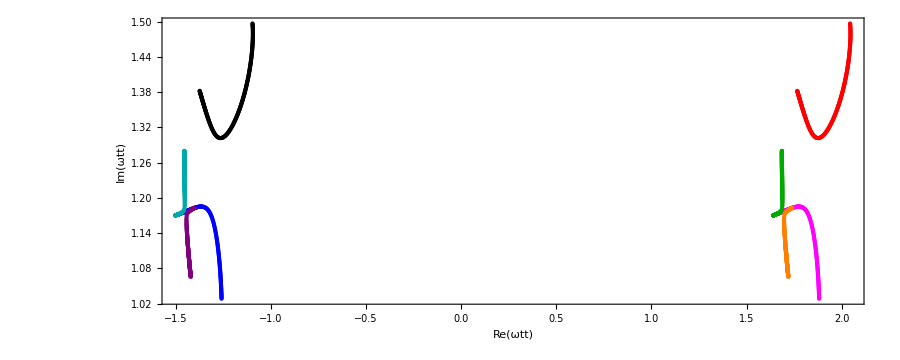
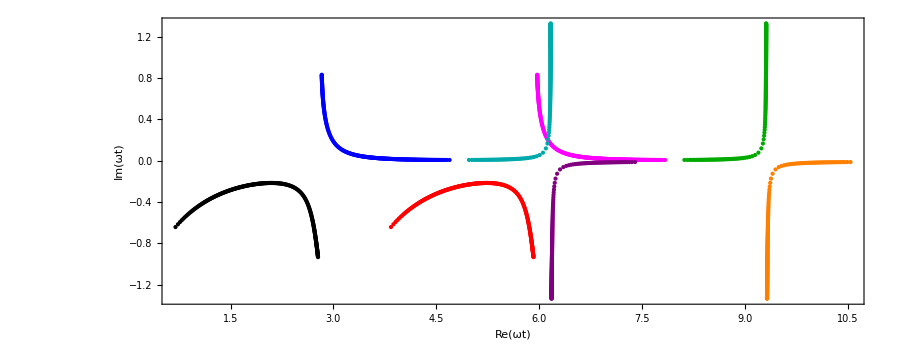
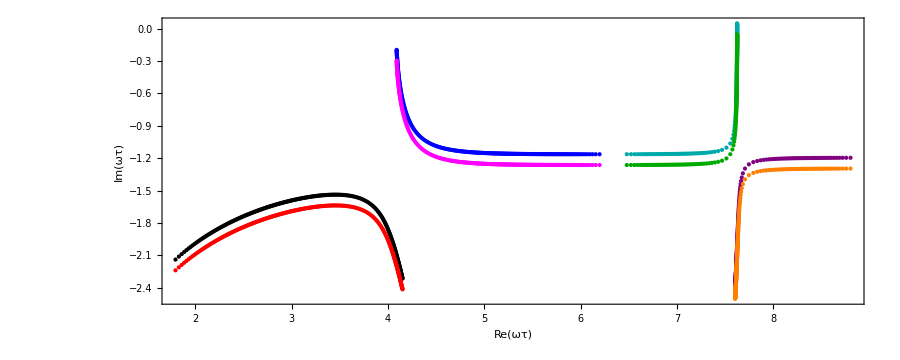
<|A→{{2,241}},B→{{2,241}},D→{{2,241}},C→{{2,241}}|>
-Graphics-
-Graphics-
-Graphics-

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;
keyColour["D",_]=Cyan;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];

Column[{
Tally/@Map[Length,selection,{2}],
Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColour[index,n]/.Missing[__]->Gray,
Tooltip[Point[ReIm[ω (t-τ)(*+Floor[ω Re[τ-t],2π]*)]],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->900
,FrameLabel->{"Re(ωtt)","Im(ωtt)"}
]
,Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColour[index,n]/.Missing[__]->Gray,
Tooltip[Point[ReIm[ω t]],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->900
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColour[index,n]/.Missing[__]->Gray,
Tooltip[Point[ReIm[ω τ+ 0.1 ⅈ 1/π Floor[ω Re[τ-t],π]]],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->900
,FrameLabel->{"Re(ωτ)","Im(ωτ)"}
]
}]
]
```

#### Classified saddles using lines-based map

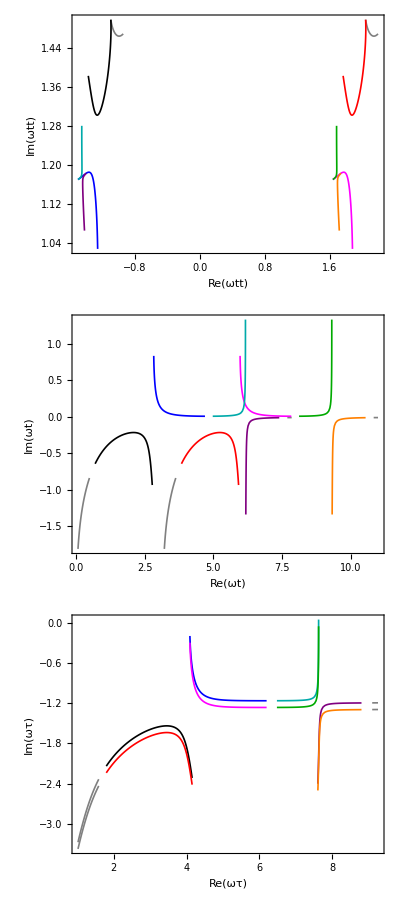

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour,d2S},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;
d2S[t_,tt_]=Derivative[0,2][S][t,tt];

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>
,"Bad"-><|1->Brown,2->Brown,3->Brown|>
|>;


selection=selectionCache=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction(*,DiscardedLabels->{"Discard"}*)];

Column[{
Show[
Table[
Values[
MapIndexed[
Function[{assoc,key},
Graphics[{
keyColour[index,key⟦1,1⟧]/.Missing[__]->Gray,Thickness[0.003],
Tooltip[Line[Values[assoc]],{index,key⟦1,1⟧}]
}]
],
DeleteMissing[Query[Transpose][
Apply[
Function[{t,τ},
ReIm[ω(t-τ)]
]
,selection[index],{2}]
],2]
]
]
,{index,Keys[selection]}]
,Frame->True,Axes->True
,PlotRangePadding->None,PlotRangeClipping->True
,ImageSize->{{1200},{700}}
,FrameLabel->{"Re(ωtt)","Im(ωtt)"}
]
,Show[
Table[
Values[
MapIndexed[
Function[{assoc,key},
Graphics[{
keyColour[index,key⟦1,1⟧]/.Missing[__]->Gray,Thickness[0.003],
Tooltip[Line[Values[assoc]],{index,key⟦1,1⟧}]
}]
],
DeleteMissing[Query[Transpose][
Apply[
Function[{t,τ},
ReIm[ω t]
]
,selection[index],{2}]
],2]
]
]
,{index,Keys[selection]}]
,Frame->True,Axes->True
,PlotRangePadding->None,PlotRangeClipping->True
,ImageSize->{{1200},{700}}
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,Show[
Table[
Values[
MapIndexed[
Function[{assoc,key},
Graphics[{
keyColour[index,key⟦1,1⟧]/.Missing[__]->Gray,Thickness[0.003],
Tooltip[Line[Values[assoc]],{index,key⟦1,1⟧}]
}]
],
DeleteMissing[Query[Transpose][
Apply[
Function[{t,τ},
ReIm[ω τ+ 0.1 ⅈ 1/π Floor[ω Re[τ-t],π]]
]
,selection[index],{2}]
],2]
]
]
,{index,Keys[selection]}]
,Frame->True,Axes->True
,PlotRangePadding->None,PlotRangeClipping->True
,ImageSize->{{1200},{700}}
,FrameLabel->{"Re(ωτ)","Im(ωτ)"}
]
}]

]
```

### Watching the Hessian for branch cuts

```mathematica
?HessianRoot
```

HessianRoot[S,t,τ] calculates the Hessian root √((2  π)^2/ⅈ^2).

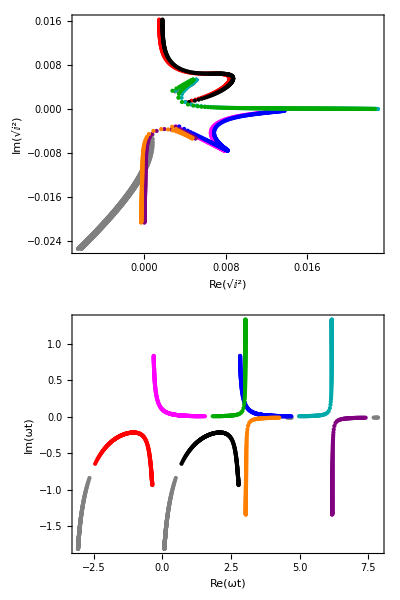

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;
keyColour["D",_]=Cyan;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction(*,DiscardedLabels->{"Discard"}*)];

Column[{
Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColour[index,n]/.Missing[__]->Gray,
Tooltip[Point[
ReIm[
1/HessianRoot[S,t,τ]+0.0001Floor[ω Re[τ-t],π]
]
],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
(*,AxesOrigin->{0,0}*)
,ImageSize->{{900},{900}}
,FrameLabel->{"Re(√(ⅈ^2))","Im(√(ⅈ^2))"}
]
,Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColour[index,n]/.Missing[__]->Gray,
Tooltip[Point[ReIm[ω t+Floor[ω Re[τ-t],2π]]],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->900
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
}]
]
```

### Demonstrating the Stokes transitions

```mathematica
?FindStokesTransitions
```

FindStokesTransitions[S,<|Ω_1→<|1→{t_11,τ_11},2→{t_12,τ_12}|>,Ω_2→<|1→{t_21,τ_21},2→{t_22,τ_22}|>,…|>] finds the set {{Ω_S},{Ω_AS},n} of the Stokes and anti-Stokes transition energies for the given set of saddle points, where Re(S) changes sign after the Ω_S and Im(S) changes sign after the Ω_AS, and n is the index of the member of the pair that should be chosen after the transition (taken as the member with a positive imaginary part of the action at the largest Ω_i in the given keys).

FindStokesTransitions[S,<|label_1→<|Ω_1→…|>|>] finds the Stokes transitions for the given set of saddle-point curve pairs, and returns them labeled with the label_i.

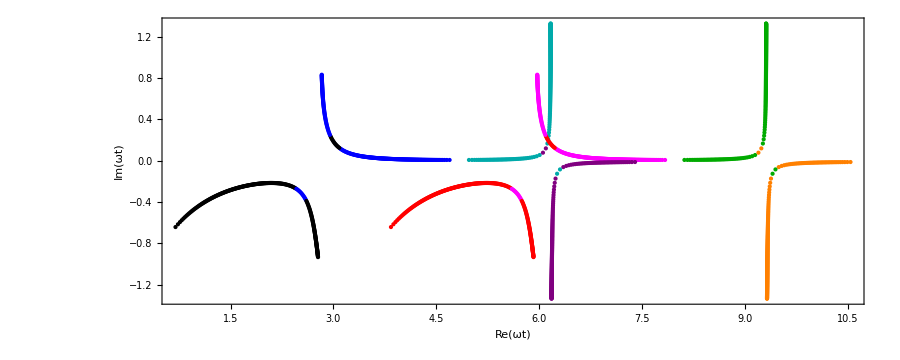
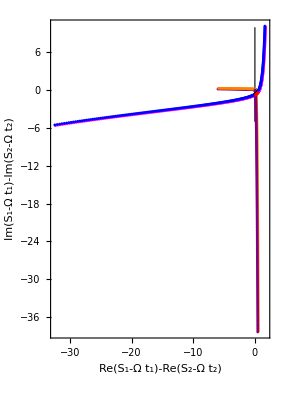
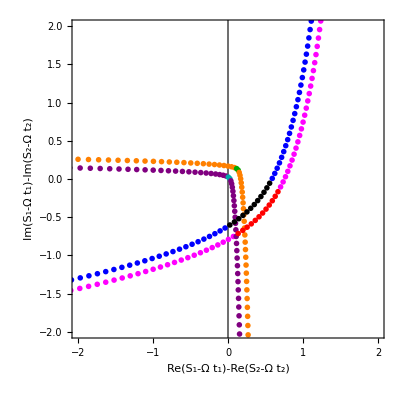
<|B→{1.767,1.8354,2},A→{1.767,1.8354,2},D→{1.1628,1.1742,1},C→{1.1628,1.1742,1}|>
-Graphics-
-Graphics-
-Graphics-

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour,transitions,secondClassifierFunction,zoomPlot},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
(*keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;*)


selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];
transitions=FindStokesTransitions[S,selection];

secondClassifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1,Ω<transitions⟦"A",1⟧],"A1",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1,transitions⟦"A",1⟧≤Ω<transitions⟦"A",2⟧],"A2",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1,transitions⟦"A",2⟧≤Ω],"A3",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0,Ω<transitions⟦"B",1⟧],"B1",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0,transitions⟦"B",1⟧≤Ω<transitions⟦"B",2⟧],"B2",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0,transitions⟦"B",2⟧≤Ω],"B3",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0,Ω<transitions⟦"C",1⟧],"C1",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0,transitions⟦"C",1⟧≤Ω<transitions⟦"C",2⟧],"C2",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0,transitions⟦"C",2⟧≤Ω],"C3",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1,Ω<transitions⟦"D",1⟧],"D1",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1,transitions⟦"D",1⟧≤Ω<transitions⟦"D",2⟧],"D2",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1,transitions⟦"D",2⟧≤Ω],"D3",
True,"Discard"
]];
keyColour=<|
"A1"-><|1->Black,2->Blue|>,"A2"-><|1->Blue,2->Black|>,"A3"-><|1->Black,2->Blue|>,
"B1"-><|1->Red,2->Magenta|>,"B2"-><|1->Magenta,2->Red|>,"B3"-><|1->Red,2->Magenta|>,
"C1"-><|1->Darker[Green],2->Orange|>,"C2"-><|1->Orange,2->Darker[Green]|>,"C3"-><|1->Darker[Green],2->Orange|>,
"D1"-><|1->Darker[Cyan],2->Purple|>,"D2"-><|1->Purple,2->Darker[Cyan]|>,"D3"-><|1->Darker[Cyan],2->Purple|>
|>;

selection=ClassifyQuantumOrbits[saddlePoints,secondClassifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];

Column[{
transitions,
Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColour[index,n]/.Missing[__]->Gray,
Tooltip[Point[ReIm[ω t]],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->900
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,zoomPlot=Show[{
Graphics[
Table[Table[{
keyColour[index,2]/.Missing[__]->Gray,
PointSize[0.005],
Tooltip[Point[ReIm[
Subtract@@Map[Function[{t,τ},
S[t,t-τ]-Ω t
]@@#&,selection[index,Ω]]
+Function[{t,τ},
0.05 ⅇ^(-ⅈ(3π)/4 Sign[Im[t]])Floor[ω Re[τ-t],π]
]@@First[selection[index,Ω]]
]],{Ω/ω,index,selection[index,Ω]}]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
],Graphics[{Thin,GrayLevel[0.2],Line[{{0,-5},{0,10}}]}]}
,Frame->True,Axes->True
,AxesOrigin->{0,0}
,ImageSize->{{900},{900}}
,FrameLabel->{"Re(S_1-Ω t_1)-Re(S_2-Ω t_2)","Im(S_1-Ω t_1)-Im(S_2-Ω t_2)"}
],
Show[zoomPlot/.{PointSize[0.005]->PointSize[0.01]},PlotRange->{2{-1,1},2{-1,1}},PlotRangeClipping->True]
}]
]
```

### Saddle-point per-pair spectrum

```mathematica
?SPAdipole
```

SPAdipole[S,prefactor,Ω,{t,τ}] returns the saddle-point approximation amplitude corresponding to action S[t,t-τ]-Ωt and the given prefactor.

SPAdipole[S,prefactor,Ω,<|1→{t_1,τ_1},2→{t_2,τ_2},…|>] returns the total harmonic-dipole contribution in the saddle-point approximation from the specified saddle points.

SPAdipole[S,prefactor,Ω,<|1→{t_1,τ_1},2→{t_2,τ_2}|>,transition] uses the given Stokes transition set to drop the relevant saddle after the anti-Stokes transition.

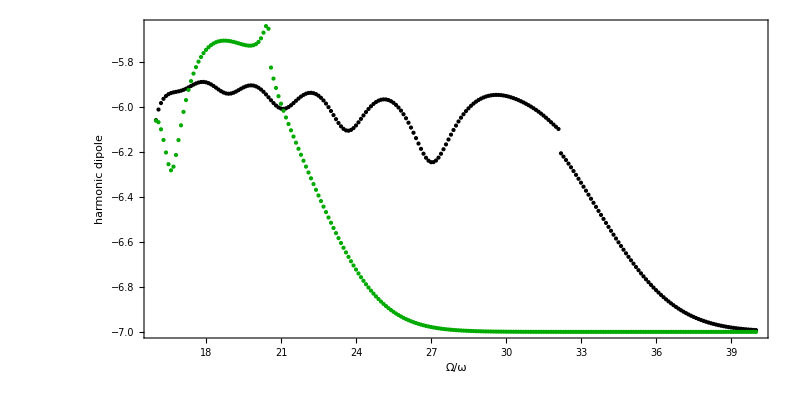

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour,transitions},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
(*And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",*)
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
(*And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",*)
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
(*keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;*)
keyColour=<|"A"->Black,"B"->Red,"C"->Darker[Green],"D"->Purple|>;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];
transitions=FindStokesTransitions[S,selection];
Show[
Graphics[
Table[Table[{
keyColour[index]/.{Missing[__]->Gray},
Tooltip[
Point[
{Ω/ω,Log10[10^-7+Norm[
SPAdipole[S,prefactor,Ω,selection[index,Ω],transitions[index]
]
]]}
],{Ω/ω,index,selection[index,Ω]}]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->800
,AspectRatio->1/2
,FrameLabel->{"Ω/ω","harmonic dipole"}
]

]
```

### Saddle-point total spectrum

```mathematica
?SPAdipole
```

SPAdipole[S,prefactor,Ω,{t,τ}] returns the saddle-point approximation amplitude corresponding to action S[t,t-τ]-Ωt and the given prefactor.

SPAdipole[S,prefactor,Ω,<|1→{t_1,τ_1},2→{t_2,τ_2},…|>] returns the total harmonic-dipole contribution in the saddle-point approximation from the specified saddle points.

SPAdipole[S,prefactor,Ω,<|1→{t_1,τ_1},2→{t_2,τ_2}|>,transition] uses the given Stokes transition set to drop the relevant saddle after the anti-Stokes transition.

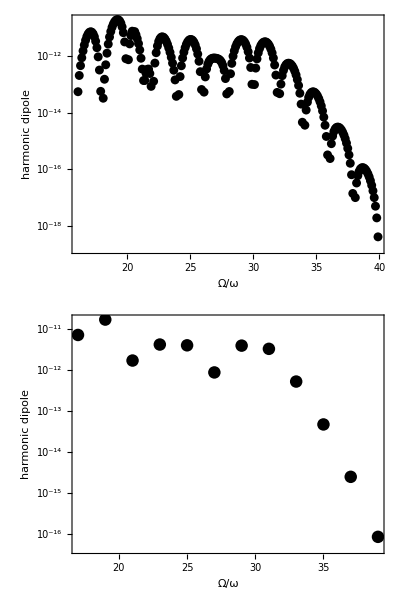

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour,transitions},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
(*keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;*)
keyColour=<|"A"->Black,"B"->Red,"C"->Darker[Green],"D"->Purple|>;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];
transitions=FindStokesTransitions[S,selection];
Column[{
ListLogPlot[
DeleteCases[
KeyValueMap[
{#1/ω,Norm[Total[#2]]^2}&
,Query[Transpose][
MapIndexed[(*calculate the dipole for each label and harmonic energy*)
With[{saddles=#1,index=#2⟦1,1⟧,Ω=#2⟦2,1⟧},
SPAdipole[S,prefactor,Ω,
If[Ω<transitions⟦index,2⟧,saddles,selection[index,Ω]⟦transitions⟦index,3⟧⟧]
]
]&,selection,{2}]]
],{n_,d_/;Abs[d]<10^-20}]
,Frame->True
,GridLines->All
,PlotStyle->Black
,ImageSize->700
,FrameLabel->{"Ω/ω","harmonic dipole"}
]
,ListLogPlot[
KeyValueMap[
{#1/ω,Norm[Total[#2]]^2}&
,Query[Transpose][
MapIndexed[(*calculate the dipole for each label and harmonic energy*)
With[{saddles=#1,index=#2⟦1,1⟧,Ω=#2⟦2,1⟧},
SPAdipole[S,prefactor,Ω,selection[index,Ω],transitions[index]
]
]&,KeySelect[Abs[#-Round[#,ω]]<0.05ω&&OddQ[Round[#/ω]]&]/@selection⟦All(*,11;;-1;;20*)⟧,{2}]]
]
,Frame->True
,GridLines->All
,PlotStyle->Black
,ImageSize->700
,FrameLabel->{"Ω/ω","harmonic dipole"}
]
}]
]
```

### Uniform Approximation per-pair spectrum

```mathematica
?UAdipole
```

UAdipole[S,prefactor,Ω,<|1→{t_1,τ_1},2→{t_2,τ_2},…|>,transition] returns the total harmonic-dipole contribution in the uniform approximation from the specified saddle points, taking the given Stokes transition set as a reference.

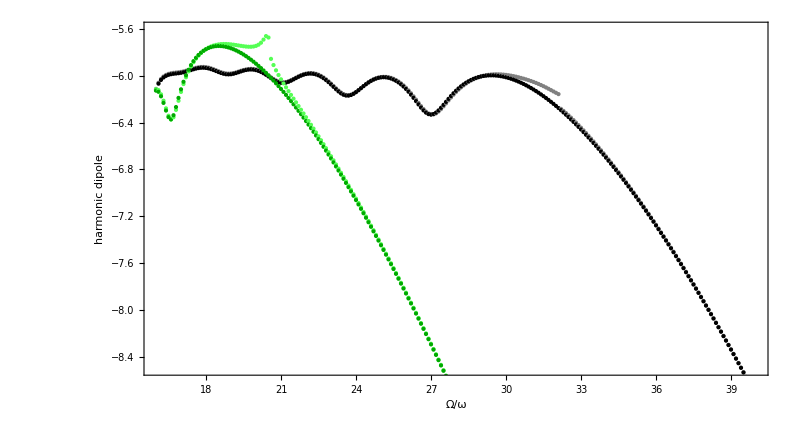

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour,transitions},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
(*And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",*)
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
(*And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",*)
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
keyColour=<|"A"->Black,"B"->Red,"C"->Darker[Green],"D"->Purple|>;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];
transitions=FindStokesTransitions[S,selection];

Column[{
Show[
Graphics[
Table[Table[{
keyColour[index]/.{Missing[__]->Gray}/.{Black->Gray,Darker[Green]->Lighter[Green]},
Tooltip[
Point[
{Ω/ω,Log10[(*10^-8.5+*)Norm[
SPAdipole[S,prefactor,Ω,selection[index,Ω],transitions[index]]
]]}
],{Ω/ω,index,selection[index,Ω]}],

keyColour[index]/.{Missing[__]->Gray},
Tooltip[
Point[
{Ω/ω,Log10[(*10^-8.5+*)Norm[
UAdipole[S,prefactor,Ω,selection[index,Ω],transitions[index]]
]]}
],{Ω/ω,index,selection[index,Ω]}]
}
,{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->800
,AspectRatio->1/1.8
,FrameLabel->{"Ω/ω","harmonic dipole"}
,PlotRange->{Automatic,{-8.5,-5.6}}
,PlotRangeClipping->True
]
}]
]
```

### Uniform Approximation total spectrum

```mathematica
?UAdipole
```

UAdipole[S,prefactor,Ω,<|1→{t_1,τ_1},2→{t_2,τ_2},…|>,transition] returns the total harmonic-dipole contribution in the uniform approximation from the specified saddle points, taking the given Stokes transition set as a reference.

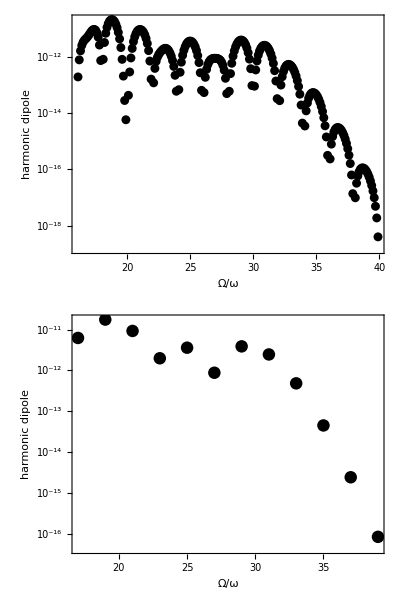

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColour,transitions},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1],"A",
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0],"C",
And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
(*keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;*)
keyColour=<|"A"->Black,"B"->Red,"C"->Darker[Green],"D"->Purple|>;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];
transitions=FindStokesTransitions[S,selection];
Column[{
ListLogPlot[
DeleteCases[
KeyValueMap[
{#1/ω,Norm[Total[#2]]^2}&
,Query[Transpose][
MapIndexed[(*calculate the dipole for each label and harmonic energy*)
With[{saddles=#1,index=#2⟦1,1⟧,Ω=#2⟦2,1⟧},
UAdipole[S,prefactor,Ω,
selection[index,Ω]
,transitions[index]]
]&,selection,{2}]]
],{n_,d_/;Abs[d]<10^-20}]
,Frame->True
,GridLines->All
,PlotStyle->Black
,ImageSize->700
,FrameLabel->{"Ω/ω","harmonic dipole"}
]
,ListLogPlot[
KeyValueMap[
{#1/ω,Norm[Total[#2]]^2+10^-20}&
,Query[Transpose][
MapIndexed[(*calculate the dipole for each label and harmonic energy*)
With[{saddles=#1,index=#2⟦1,1⟧,Ω=#2⟦2,1⟧},
UAdipole[S,prefactor,Ω,
selection[index,Ω]
,transitions[index]]
]&,KeySelect[Abs[#-Round[#,ω]]<0.05ω&&OddQ[Round[#/ω]]&]/@selection,{2}]]
]
,Frame->True
,GridLines->All
,PlotStyle->Black
,ImageSize->700
,FrameLabel->{"Ω/ω","harmonic dipole"}
]
}]
]
```

### Testing the degrading of UAdipole to SPAdipole when there’s too few or too many solutions

The classifierFunction below has been explicitly chosen so that the spectrum gets damaged: the ‘keeper’ member of the A pair has been cut off by asking for Im(ω t)<0.5, and the lower Re(ω t) limit of the C pair has been chosen too low so that there is an extra saddle intruding upon the set.

FindStokesTransitions::saddleno: FindStokesTransitions called with 55 of 241 saddle-point sets of length different from 2, with set length structure {{2,186},{1,55}}. Excluding those sets from the calculation.

FindStokesTransitions::saddleno: FindStokesTransitions called with 219 of 241 saddle-point sets of length different from 2, with set length structure {{3,33},{2,22},{1,186}}. Excluding those sets from the calculation.

SPAdipole::wrongno: SPAdipole called with a Stokes transition but with an input association of length 3 at harmonic energy Ω=0.912. Reverting to unstructured evaluation.

UAdipole::saddleno: UAdipole called with 3 time pairs at Ω=0.912. Reverting to the saddle-point approximation for this set.

SPAdipole::wrongno: SPAdipole called with a Stokes transition but with an input association of length 3 at harmonic energy Ω=0.9177. Reverting to unstructured evaluation.

UAdipole::saddleno: UAdipole called with 3 time pairs at Ω=0.9177. Reverting to the saddle-point approximation for this set.

SPAdipole::wrongno: SPAdipole called with a Stokes transition but with an input association of length 3 at harmonic energy Ω=0.9234. Reverting to unstructured evaluation.

General::stop: Further output of SPAdipole::wrongno will be suppressed during this calculation.

UAdipole::saddleno: UAdipole called with 3 time pairs at Ω=0.9234. Reverting to the saddle-point approximation for this set.

General::stop: Further output of UAdipole::saddleno will be suppressed during this calculation.

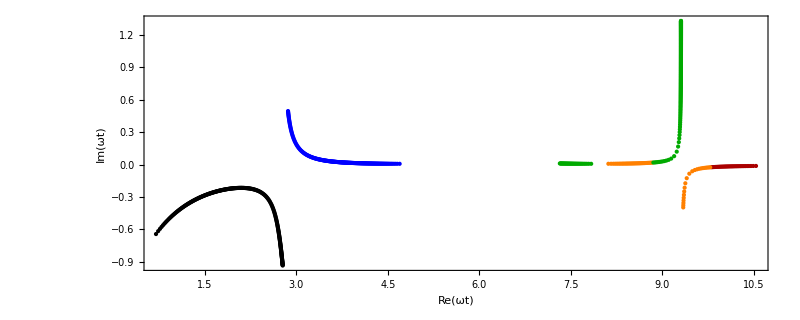
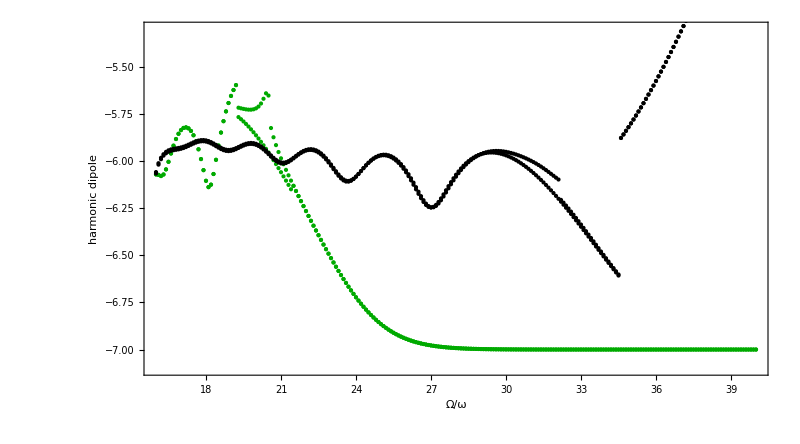
<|A→{1.767,1.8354,2},C→{1.1628,1.1742,1}|>
-Graphics-
-Graphics-

```mathematica
Block[{ω,Ip,κ,U,γ,selection,classifierFunction,sortingFunction,keyColourPoints,keyColourSpectrum,transitions},
{ω,Ip,κ,U,γ}={ω,Ip,√(2Ip),F^2/(4 ω^2),(κ ω)/F}//.parameters;

classifierFunction=Function[{t,τ,Ω},Which[
And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==-1,Im[ω t]<0.5],"A",
(*And[1.65<ω Re[τ]<6.3,Floor[ω Re[t-τ],π]/π==0],"B",*)
And[5.654<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==0,Im[ω t]>-0.4],"C",
(*And[6.3<ω Re[τ]<8.9,Floor[ω Re[t-τ],π]/π==-1],"D",*)
True,"Discard"
]];
sortingFunction=Function[list,SortBy[list,Function[Re[ω #⟦1⟧-Floor[ω Re[#⟦1⟧-#⟦2⟧],2π]]]]];
(*keyColour=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange,3->Darker[Red]|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;*)
keyColourPoints=<|"A"-><|1->Black,2->Blue|>,"B"-><|1->Red,2->Magenta|>,"C"-><|1->Darker[Green],2->Orange,3->Darker[Red]|>,"D"-><|1->Darker[Cyan],2->Purple|>|>;
keyColourSpectrum=<|"A"->Black,"B"->Red,"C"->Darker[Green],"D"->Purple|>;

selection=ClassifyQuantumOrbits[saddlePoints,classifierFunction,sortingFunction,DiscardedLabels->{"Discard"}];
transitions=FindStokesTransitions[S,selection];


Column[{
transitions,
Show[
Graphics[
Table[Table[{
KeyValueMap[
Function[{n,t,τ},
{keyColourPoints[index,n]/.Missing[__]->Gray,
Tooltip[Point[ReIm[ω t]],{Ω/ω,index,n,ω{t,τ},1/π Floor[ω Re[t-τ],π]}]}
]@*Apply[Sequence]@*Flatten@*List
,selection[index,Ω]]
},{Ω,Keys[selection[index]]}],{index,Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->800
,FrameLabel->{"Re(ωt)","Im(ωt)"}
]
,Show[
Graphics[
Table[Table[{
keyColourSpectrum[index]/.{Missing[__]->Gray}(*/.{Black->Gray,Darker[Green]->Lighter[Green]}*),
Tooltip[
Point[
{Ω/ω,Log10[10^-7+Norm[
SPAdipole[S,prefactor,Ω,selection[index,Ω],transitions[index]]
]]}
],{Ω/ω,index,ω selection[index,Ω],"SPA"}],

keyColourSpectrum[index]/.{Missing[__]->Gray},
Tooltip[
Point[
{Ω/ω,Log10[10^-7+Norm[
UAdipole[S,prefactor,Ω,selection[index,Ω],transitions[index]]
]]}
],{Ω/ω,index,ω selection[index,Ω],"UA"}]
}
,{Ω,Keys[selection[index]]}],{index,Reverse@Keys[selection]}]
]
,Frame->True,Axes->True
,ImageSize->800
,AspectRatio->1/1.8
,FrameLabel->{"Ω/ω","harmonic dipole"}
,PlotRange->{Automatic,{-7.1,-5.3}}
,PlotRangeClipping->True
]
}]
]
```

The spectrum for this saddle-point classification is very ugly, but it does exactly what it needs to be doing.

For Ω≲19.5ω, the C set gets a third saddle from what ought to be B, and UAdipole surrenders the calculation to SPAdipole, so the two match at low Ω for the green curve.

For Ω≲19.5ω on the C set, there is a third saddle contributing to SPAdipole, so it’s displaying a bigger dipole with more contributions (and also more interference). This saddle gets dropped after Ω=19.4ω, which gives the discontinuity there.

For Ω≳35ω, the wanted root (A,1) is no longer present. The UAdipole call surrenders the calculation to SPA dipole and the two match on the black curve after Ω=34.6ω.

For Ω≳35ω on the SPA branch it’s getting a malformed input so it ignores the Stokes transition and evaluates the saddle it’s been given, which is the divergent one at Im(t)<0, Im(S(t))<0, and this gives the exponential growth after Ω=34.6ω

For Ω≳21.5ω, the C set loses the Im(t)<0 root, which is the unwanted Im(S(t))<0 one, so everything is mostly fine. Here the SPAdipole call has a single saddle so it issues a warning that it’s reverting to unstructured evaluation, but this does not change the outcome.

For Ω≳21.5ω on the C set, the UAdipole call has a single saddle so it reverts to unstructured SPAdipole, which is a good approximation here, but this causes a slight discontinuity at Ω=21.5ω; both curves match after that.